```mathematica
Plot3D[{CubeRoot[x^2]+CubeRoot[y^2]==1,x^2+y^2==1/4},{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
epsilon = 1.0
While[(1.0+0.5*epsilon) ≠ 1.0, epsilon = 0.5*epsilon;Print[epsilon]]
```

1.

0.5

0.25

0.125

0.0625

0.03125

0.015625

0.0078125

0.00390625

0.00195313

0.000976563

0.000488281

0.000244141

0.00012207

0.0000610352

0.0000305176

0.0000152588

7.62939×10^-6

3.8147×10^-6

1.90735×10^-6

9.53674×10^-7

4.76837×10^-7

2.38419×10^-7

1.19209×10^-7

5.96046×10^-8

2.98023×10^-8

1.49012×10^-8

7.45058×10^-9

3.72529×10^-9

1.86265×10^-9

9.31323×10^-10

4.65661×10^-10

2.32831×10^-10

1.16415×10^-10

5.82077×10^-11

2.91038×10^-11

1.45519×10^-11

7.27596×10^-12

3.63798×10^-12

1.81899×10^-12

9.09495×10^-13

4.54747×10^-13

2.27374×10^-13

1.13687×10^-13

5.68434×10^-14

2.84217×10^-14

```mathematica
indexer = 0;
summ = 0.;
a[0] = 1.;
a[1]=0.5;
a[n_]:=2^-n;
While[summ<2.,
summ = summ + a[indexer];
Print[indexer," ", summ]; 
 indexer++;
]
```

0 1.

1 1.5

2 1.75

3 1.875

4 1.9375

5 1.96875

6 1.98438

7 1.99219

8 1.99609

9 1.99805

10 1.99902

11 1.99951

12 1.99976

13 1.99988

14 1.99994

15 1.99997

16 1.99998

17 1.99999

18 2.

19 2.

20 2.

21 2.

22 2.

23 2.

24 2.

25 2.

26 2.

27 2.

28 2.

29 2.

30 2.

31 2.

32 2.

33 2.

34 2.

35 2.

36 2.

37 2.

38 2.

39 2.

40 2.

41 2.

42 2.

43 2.

44 2.

45 2.

46 2.

```mathematica
methodBisection[f_, g_,a_,b_,epsil_:epsilon]:=(
Clear[mid];
Clear[start];
Clear[final];
start=a;
final=b;
res[x_]:=f[x]-g[x];
While[Abs[start-final]>epsil,
{mid=(start+final)/2,
If[Sign[res[start]]≠Sign[res[final]],
If[Sign[res[start]]≠Sign[res[mid]],
(final=mid;
mid=(start+final)/2;),
(start=mid;mid=(start+final)/2;)]]};];Return[mid]) //N
```

```mathematica
(*Задание 1*)
y1[x_]:= x-1;
y2[x_]:=0;
```

```mathematica
res1 = methodBisection[y1,y2, -1, 5]
```

1.00002

```mathematica
Print[res1]
```

1.00002

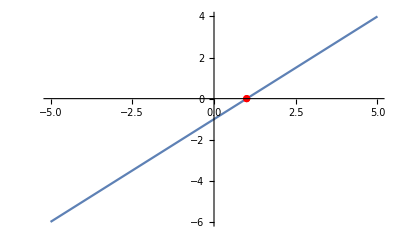

```mathematica
(*так мы нашли корень х-1=0, 1.00002, более известный как 1*)
plt1 = Plot[y1[x], {x, -5, 5}];
pltPoint = ListPlot[{{res1,y1[res1]}},PlotStyle-> Red];
Show[plt1, pltPoint]
```

1.5

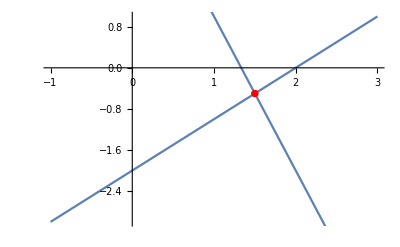

```mathematica
(*Задание 2*)
y3[x_]:=x-2;
y4[x_]:=-3x+4;
plt3 = Plot[y3[x], {x, -1, 3}];
plt4 = Plot[y4[x], {x,-1,3}];
res2  = methodBisection[y3,y4, -1, 5, 0.00001];
Print[res2]
plt34= ListPlot[{{res2, y3[res2]}},PlotStyle-> Red];
Show[plt3,plt4,plt34]
```

```mathematica
(*корень - х=1,5*)
```

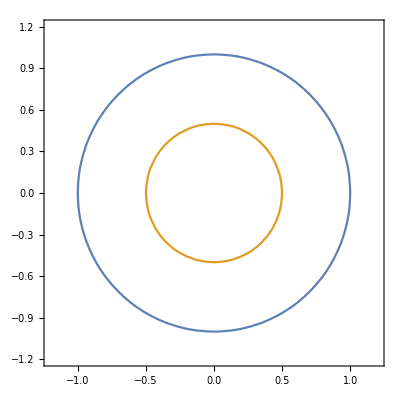

```mathematica
ContourPlot[{x^2+y^2==1, x^2+ y^2==1/4}, {x,-1.2,1.2},{y,-1.2,1.2}]
```

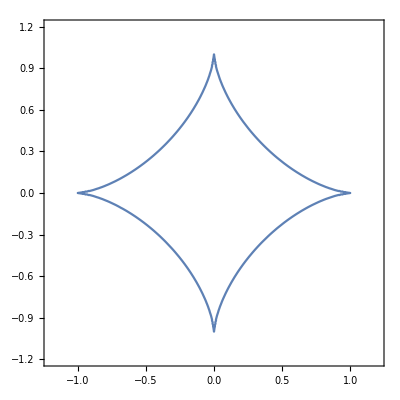

```mathematica
ContourPlot[CubeRoot[x^2]+CubeRoot[y^2]==1, {x,-1.2,1.2},{y,-1.2,1.2}]
```

```mathematica
methodBisection[f_, g_,a_,b_,epsil_:0.0001]:=(
Clear[mid];
Clear[start];
Clear[final];
start=a;
final=b;
res[x_]:=f[x]-g[x];
While[Abs[start-final]>epsil,
{mid=(start+final)/2,
If[Sign[res[start]]≠Sign[res[final]],
If[Sign[res[start]]≠Sign[res[mid]],
(final=mid;
mid=(start+final)/2;),
(start=mid;mid=(start+final)/2;)]]};];Return[mid]) //N
```

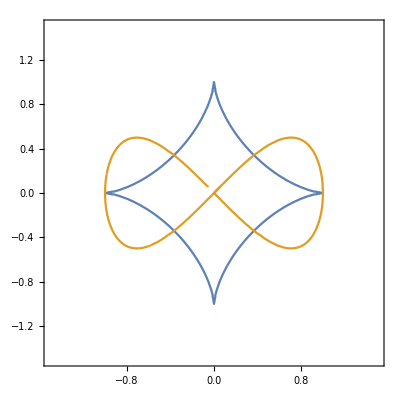

0.363281

{{y→-0.343914},{y→0.343914}}

{y→0.343914}

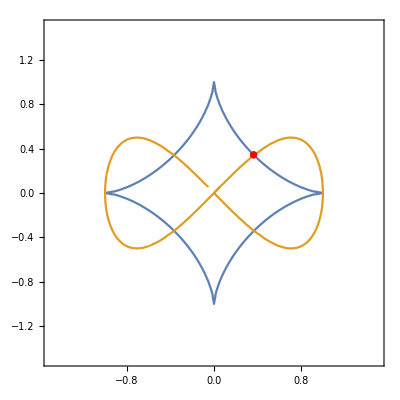

```mathematica
(*Задание 0
выразим обе функции относительно корня 3 степени из у^2*)
func1[x_]:=1 - (x^2)^(1/3);(*астроида*)
func2[x_]:=(x^2-x^4)^(1/3);(*восьмерка*)
pltF0 = ContourPlot[{(x^2)^(1/3)+(y^2)^(1/3)==1, (y^2)==x^2-x^4},{x,-1.5,1.5}, {y,-1.5,1.5}];

Show[pltF0]
resF0= methodBisection[func1, func2, 0, 2, 0.01];
Print[resF0]
yRes0 = Solve[(resF0^2)^(1/3)+(y^2)^(1/3)==1 ,y]
yFRes0 = Part[yRes0, 2]
pltF0P = ListPlot[{{resF0, 0.34391394563092303}},PlotStyle->Red];
Show[pltF0, pltF0P]
```

```mathematica
(*найдена точка пересечения кривых с абсциссой - х=0.36636829376220703, расположенная в первом квадранте и отличная от А(1,0)*)
```

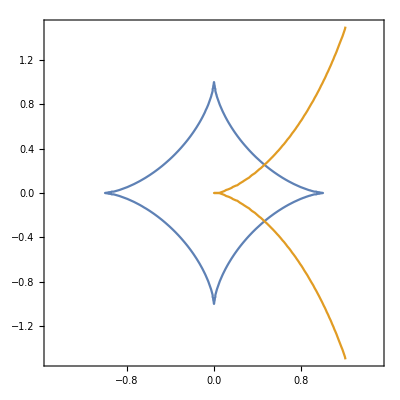

```mathematica
(*Задание 1
снова выразим обе кривые как функции у в степени 2/3 от х*)
func3[x_]:=(x^3/(2-x))^(1/3);(*циссоида*)

pltF1= ContourPlot[{(y^2)^(1/3)+(x^2)^(1/3)==1,y^2==x^3/(2-x)},{x, -1.5,1.5},{y, -1.5,1.5}]
```

```mathematica
resF1= methodBisection[func1, func3, 0, 1, 0.000001];
Print[resF1]
```

0.463175

{{y→-0.254276},{y→0.254276}}

{y→0.254276}

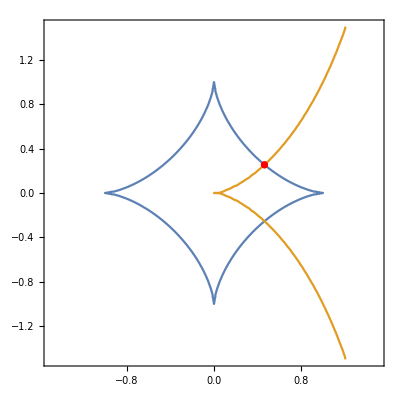

```mathematica
yRes1 = Solve[(resF1^2)^(1/3)+(y^2)^(1/3)==1 ,y]
yFRes1 = Part[yRes1, 2]
pltF1P = ListPlot[{{0.4631767272949219, 0.25410963276666804}},PlotStyle->Red];
Show[pltF1, pltF1P]
```

```mathematica
(*найдена точка пересечения кривых с абсциссой х=0.46337890625 в первом квадранте*)
```

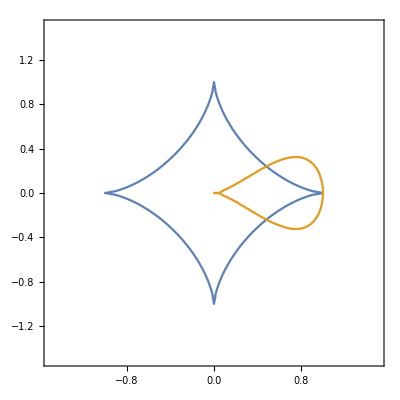

```mathematica
(*Задание 2*)
func4[x_]:=(x^3(1-x))^(1/3);(*жемчужина*)
pltF2= ContourPlot[{(y^2)^(1/3)+(x^2)^(1/3)==1,y^2==x^3(1-x)},{x, -1.5,1.5},{y, -1.5,1.5}]
```

```mathematica
resF2= methodBisection[func1, func4, 0, 1, 0.00000001];
Print[resF1]
```

0.463175

{{y→-0.240163},{y→0.240163}}

{y→0.240163}

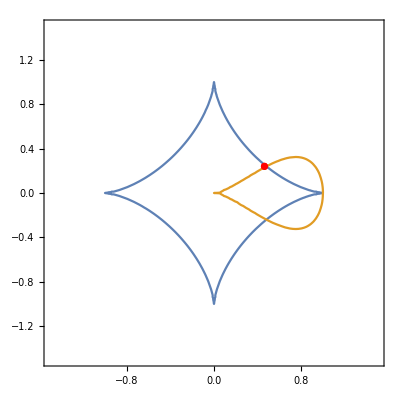

```mathematica
yRes2= Solve[(resF2^2)^(1/3)+(y^2)^(1/3)==1 ,y]
yFRes2 = Part[yRes2, 2]
pltF2P = ListPlot[{{0.46317529678344727, 0.2401627850112635}},PlotStyle->Red];
Show[pltF2, pltF2P]
```

```mathematica
(*найдена точка пересечения кривых с абсциссой х=0.46317529678344727 в первом квадранте*)
```

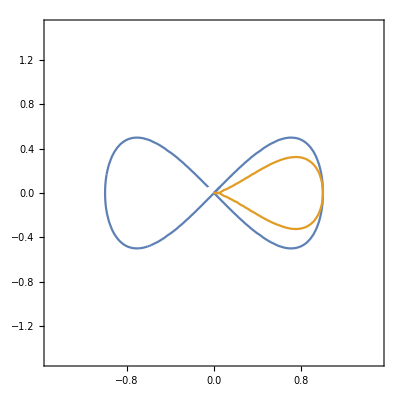

```mathematica
(*Задание 4*)
func2[x_]:=(x^2-x^4)^(1/3);(*восьмерка*)
func4[x_]:=(x^3(1-x))^(1/3);(*жемчужина*)
pltF3= ContourPlot[{(y^2)==x^2-x^4,y^2==x^3(1-x)},{x, -1.5,1.5},{y, -1.5,1.5}]
```

```mathematica
methodBisection[f_, g_,a_,b_,epsil_:0.0001]:=(
Clear[mid];
Clear[start];
Clear[final];
start=a;
final=b;
res[x_]:=f[x]-g[x];
While[Abs[start-final]>epsil,
{mid=(start+final)/2,
If[Sign[res[start]]≠Sign[res[final]],
If[Sign[res[start]]≠Sign[res[mid]],
(final=mid;
mid=(start+final)/2;),
(start=mid;mid=(start+final)/2;)]]};];Return[mid]) //N
```

```mathematica
resF3= methodBisection[func2, func4, 0, 2, 0.001];
Print[resF3]
```

1.00049

1.00049

{{y→0.-0.0312691 ⅈ},{y→0.+0.0312691 ⅈ}}

{y→0.+0.0312691 ⅈ}

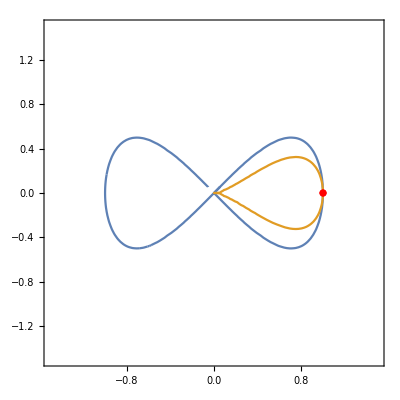

```mathematica
yRes3= Solve[y^2==resF3^2-resF3^4,y]
yFRes3 = Part[yRes3, 2]
pltF3P = ListPlot[{{1.00048828125, 0.}},PlotStyle->Red];
Show[pltF3, pltF3P]
```

```mathematica
resF32= methodBisection[func2, func4, -0.01, 0.01, 0.0001];
Print[resF32]
```

-0.00996094

```mathematica
yRes32= Solve[y^2==resF32^2-resF32^4,y]
Print[yRes32]
pltF32P = ListPlot[{{-0.0099609375, 0.009960443324258252},PlotStyle->Red},PlotStyle->Red];
```

{{y→-0.00996044},{y→0.00996044}}

{{y→-0.00996044},{y→0.00996044}}

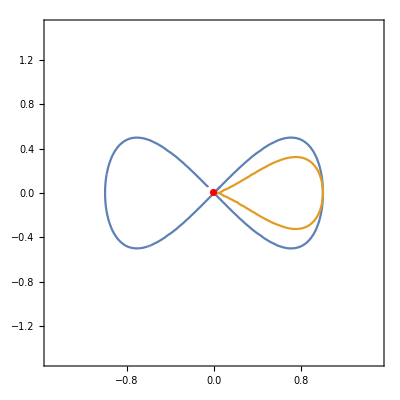

```mathematica
Show[pltF3,pltF32P]
```

```mathematica
(*найдена точка пересечения кривых с абсциссой х=1.00048828125 в первом квадранте, также есть точка пересечения с абсциссой 0 *)
```

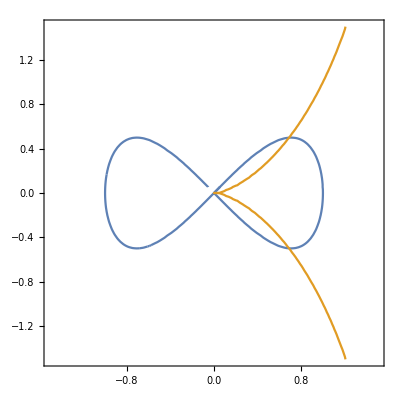

```mathematica
(*Задание 3*)

func2[x_]:=(x^2-x^4)^(1/3);(*восьмерка*)
func3[x_]:=(x^3/(2-x))^(1/3);(*циссоида*)
pltF4= ContourPlot[{(y^2)==x^2-x^4,y^2==x^3/(2-x)},{x, -1.5,1.5},{y, -1.5,1.5}]
```

```mathematica
resF4= methodBisection[func2, func3, 0.001, 1, 0.0001];
Print[resF4]
```

0.68888

```mathematica
yRes4= Solve[y^2==resF4^2-resF4^4,y]
Print[yRes4]
pltF4P = ListPlot[{{0.6888795471191406, 0.49935213379342186},PlotStyle->Red},PlotStyle->Red];
```

{{y→-0.499352},{y→0.499352}}

{{y→-0.499352},{y→0.499352}}

```mathematica
Show[pltF4,pltF4P]
```

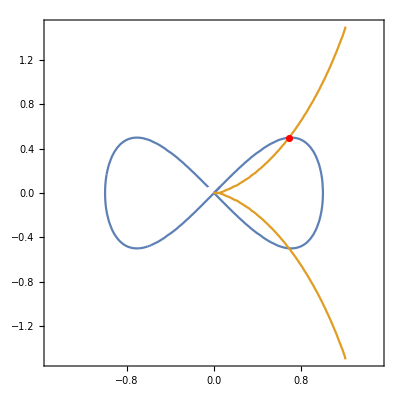

```mathematica
(*найдена точка пересечения кривых с абсциссой х=0.6888795471191406 в первом квадранте, также есть точка пересечения с абсциссой 0 *)
```